# Constrained method

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="ConstrainedNewMethod";
```

## Test Points {line1, line2, pyrf12}

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-4,30-4}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

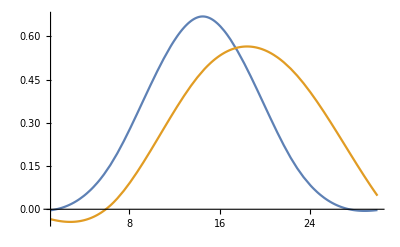

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[4,1,1]][x],pyrf12[[4,2,1]][x]},{x,1,30}]
```

## Pyramidal Flow 1D (PyrFlow1D)

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status, and counter e}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status and e} *)
PyrUpgrade1D[{v1_,v2_,status_,e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Block[{fric1,fric2,p1, p2, c,d1,d2,dv1,dv2},(

n=1;

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=1*dfline1'[p1];
fric2=1*dfline2'[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, If[e<n,Return[{v1,v2,"sign",e+1}],Return[{0.,0.,"sign",e}]]];

(* magnitud *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),If[e<n,Return[{v1,v2,"mag",e+1}],Return[{0.,0.,"mag",e}]]];

(* Change of sign during iteration *)
(*If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),If[e<2,Return[{v1,v2,"flip",e+1}],Return[{0.,0.,"flip",e}]]];*)

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

If[e<n,{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.01,"converged","ok"],e},Return[{0.,0.,status,e}]]

)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)
PyrUpgrade1D[{v1_,v2_,"sign",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"sign",e}];

PyrUpgrade1D[{v1_,v2_,"mag",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"mag",e}];

PyrUpgrade1D[{v1_,v2_,"flip",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"flip",e}];
```

### Test

```mathematica
(* initial values *)
{v1, v2,status,e}={0.2,3.,"ok",0.};
i=0;
p=10.;
```

```mathematica
n=3;
status="ok";
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)

{v1,v2,status,e}=PyrUpgrade1D[{v1,v2,status,e},p, pyrf12[[n]],0.01,noteBookMode]
```

{0.99349,2.86729,ok,0.}

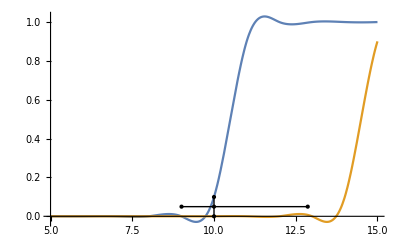

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[n]]]
```

### PyrFlow1D

```mathematica
(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 10 and -10 *)

newValues[i_,{v1_,v2_,status_,e_},newv0_,"ConstrainedNewMethod"]:=Block[{v,r,rs},(
v=v1+v2;
n=1;

If[e>=n,
Return[{{0.,0.}}];
];

If[v≠0. && status=="ok",
Table[
r=RandomReal[];
{r,1-r}*v
,{j,i}]
,
newv0
]

)]
```

```mathematica
(* We create the list of values in case v=0 *)
r=RandomReal[];
rangev0=Range[0,5,0.2];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];
```

```mathematica
nV=newValues[10,{1.,1.,"sign",1.},newv0,"ConstrainedNewMethod"]
Total/@nV
```

{{0.,0.}}

{0.}

```mathematica
(* This will give back a value that converged or is on "ok" status. If not, error is returned and {v1,v2} goes back to 0. *)

pickNewValue[tableNewVals_,"ConstrainedNewMethod"]:=Block[{newValCon,newValAny},(

newValCon=Select[tableNewVals,(#[[3]]==("converged")&& #[[1]]*#[[2]]>0 && Abs[#[[2]]+#[[1]]]<15)&,1];
newValAny=Select[tableNewVals,(#[[1]]*#[[2]]>0 && Abs[#[[2]]+#[[1]]]<15)&,1];

If[newValCon=={}&&newValAny=={},
tableNewVals[[1]]
,

If[newValCon=={},

If[newValAny[[1,3]]!="converged",
newValAny[[1]],
Flatten[{0.,0.,"fakeconverged",newValAny[[1,4]]+1}]
],

newValCon[[1]]
]

]
)]
```

```mathematica
threshold=0.001;
n=3;
p0=10;
i=10;

updateValues={0.,0.,"ok",0.};

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)

nV=newValues[10,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNV=Table[
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),noteBookMode]

,{j,1,i}];

tValues
,{v,nV}];

sol=pickNewValue[tableNV,"ConstrainedNewMethod"]
```

{0.104781,3.87427,converged,0.}

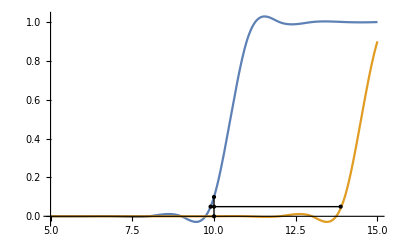

```mathematica
(* see *)
seePlot[p0,5,sol[[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_, p0_,listv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c, updateValues,nV,tableNewValues,tValues},(

n=1;

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Do[


(* Flag to stop when e≥n *)
If[updateValues[[4]]<n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],n}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,updateValues[[1;;4]],listv0,"ConstrainedNewMethod"];
(* compute at this scale, using current motion estimate *)

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[
tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"]

,{j,1,i}];
tValues
,{v,nV}];

(* We only update updateValues with the tValue that converged *)
updateValues=pickNewValue[tableNewValues,"ConstrainedNewMethod"];


c=c-1;
,{f,1,Length[pyrfunctions]}];

updateValues[[1;;3]]
)];
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
(* Initializing values *)
{v1, v2}={0.,0.};
i=10;
p=15;

(* m-> max lvl, n-> min lvl *)
m=1;
n=4;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i, p,newv0,pyrf12[[m;;n]],0.0001*2^(-m+1),noteBookMode]
{Total[{v1,v2}],status}
```

{0.,0.,sign}

{0.,sign}

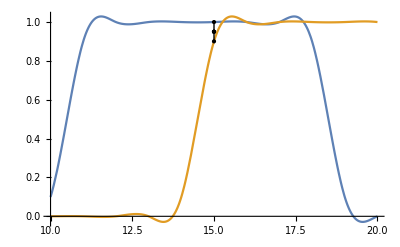

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[m]]]
```

## Graphics for All pixels

### All Pixel Graphics

#### Test

{{0.,0.,sign,1},{0.,0.,sign,2},{0.,0.,sign,3},{2.61012,1.40153,mag,4},{1.67923,2.33651,mag,5},{0.,0.,sign,6},{3.15418,0.846962,mag,7},{1.99495,2.00505,converged,8},{0.00914599,3.99085,converged,9},{0.120054,3.87995,converged,10},{0.553809,3.44619,converged,11},{1.5,2.5,converged,12},{2.5,1.5,converged,13},{3.44618,0.553818,converged,14},{0.,0.,sign,15},{0.,0.,sign,16},{0.,0.,sign,17},{0.0970138,3.90299,converged,18},{0.553818,3.44618,converged,19},{1.5,2.5,converged,20},{2.5,1.5,converged,21},{3.44619,0.553809,converged,22},{3.88679,0.113206,converged,23},{2.01112,1.98889,converged,24},{2.00611,1.99404,converged,25},{3.98364,0.0175005,converged,26},{0.,0.,sign,27},{0.,0.,sign,28},{0.616824,7.34925,mag,29},{0.,0.,mag,30}}

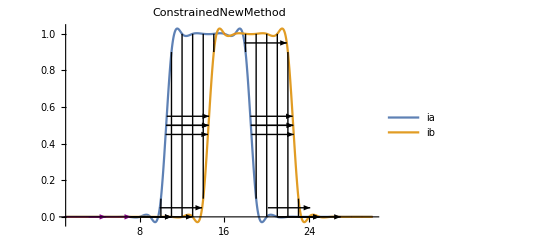

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[newv0,Range[1,Length[line1]],pyrf12[[1;;4]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[newv0,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

```mathematica
ListAnimate[pixelIterGraphics[10,15,newv0,4, 4,pyrf12[[1;;4]],0.001,"ConstrainedNewMethod"]];
```

## Graphics for One pixel

```mathematica
pickNewValueIter[tableIterNewVals_,"ConstrainedNewMethod"]:=Block[{newIterValCon,newIterValAny},(
newIterValCon=Select[tableIterNewVals,(Last[#][[3]]==("converged")&&Last[#][[1]]*Last[#][[2]]>0 && Abs[Last[#][[2]]+Last[#][[1]]]<15)&,1];
newIterValAny=Select[tableIterNewVals,(Last[#][[1]]*Last[#][[2]]>0 && Abs[Last[#][[2]]+Last[#][[1]]]<15)&,1];

If[newIterValCon=={}&&newIterValAny=={},
tableIterNewVals[[1]]
,

If[newIterValCon=={},

If[Last[newIterValAny[[1]]][[3]]≠"converged",
newIterValAny[[1]],
Join[newIterValAny[[1]],{Flatten[{0.,0.,"fakeconverged",Last[newIterValAny[[1]]][[4]]+1}]}]
]
,
newIterValCon[[1]]
]

]

)]
```

```mathematica
i=10;
p0=10;
threshold=0.001;
n=3;
updateValues={0.,0.,"ok",0.};
```

```mathematica
(* Flag to stop when e≥2 *)
If[updateValues[[4]]<2,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],2}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 5 and -5 *)
nV=newValues[10,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"][[All,1;;3]]

Last[goodValIter]
```

{{0.0243943,3.61968,ok},{0.0430796,3.69344,ok},{0.0573774,3.74517,ok},{0.068307,3.78285,ok},{0.0766545,3.81078,ok},{0.0830253,3.83168,ok},{0.0878844,3.84741,ok},{0.0915886,3.85928,ok},{0.0944114,3.86826,converged},{0.0965616,3.87506,converged}}

{0.0965616,3.87506,converged}

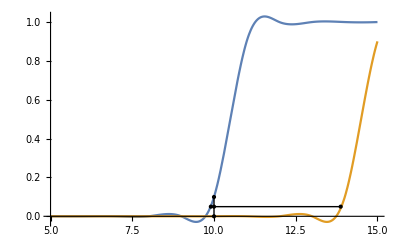

```mathematica
(* see *)
seePlot[p0,5,Last[goodValIter][[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_, p0_,newv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c,updateValues,newVals,tableNewValues,tValues,iterTable,goodValIter,nV},(

n=1;

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Table[

(* Flag to stop when e≥n *)
If[updateValues[[4]]<n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],n}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];


tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

c=c-1;

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"];
updateValues=Last[goodValIter];

goodValIter[[All,1;;3]]
,{f,1,Length[pyrfunctions]}]

)];
```

#### Test

```mathematica
Table[
PyrFlow1D[10, p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]
,{p,1,30}]
```

{{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{1.53403,2.47762,mag},{0.,0.,mag},{0.,0.,sign},{1.00307,2.99702,converged},{0.995203,3.0048,converged},{1.99382,2.00618,converged},{0.113194,3.88681,converged},{0.553809,3.44619,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44618,0.553818,converged},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.100165,3.89984,converged},{0.553818,3.44618,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44619,0.553809,converged},{3.87618,0.123821,converged},{0.997535,3.00238,converged},{2.00501,1.99513,converged},{3.98495,0.0162074,converged},{0.,0.,sign},{0.,0.,mag},{0.,0.,sign},{0.,0.,sign}}

```mathematica
Table[
PyrFlow1DIter[10,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{3.9647,0.0469588,sign},{0.519184,3.49655,mag},{0.,0.,sign},{0.991663,3.00852,converged},{1.99603,2.00396,converged},{2.99509,1.00491,converged},{0.102094,3.89791,converged},{0.553809,3.44619,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44618,0.553818,converged},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.0958818,3.90412,converged},{0.553818,3.44618,converged},{1.5,2.5,converged},{2.5,1.5,converged},{3.44619,0.553809,converged},{3.88974,0.110259,converged},{2.98916,1.01084,converged},{2.98456,1.0154,converged},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{1.50806,6.46167,mag},{0.,0.,sign}}

```mathematica
Table[
PyrFlow1D[10, p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]==PyrFlow1DIter[10,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{True,True,True,False,False,True,False,False,False,False,False,True,True,False,True,True,True,False,False,True,True,False,False,False,False,False,True,False,False,True}

#### Test

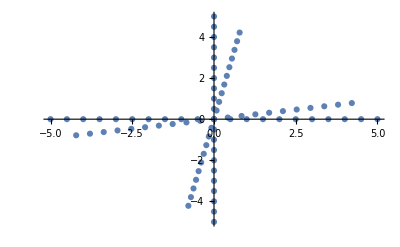

```mathematica
(* List of initial values we are going to try *)
ListPlot[newv0]
```

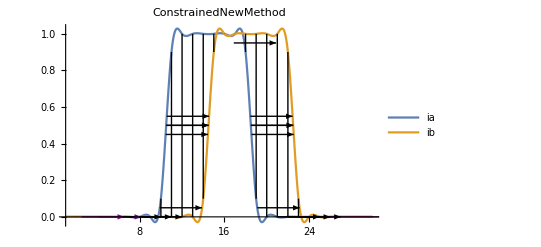

```mathematica
seeAllLine[newv0,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

```mathematica
(* Creating list of initial Values *)
rangev0=Range[0,5,0.5];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
```

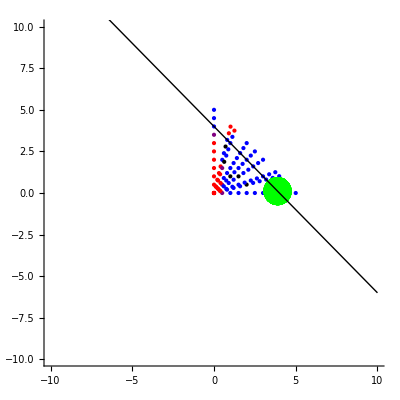
-Graphics-ConstrainedNewMethod

```mathematica
lvlmin=1;
lvlmax=3;
p=15;
dis=4;

mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,p,listv0,dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]
```

```mathematica
lvlmin=3;
lvlmax=3;
p=14;
mode="ConstrainedNewMethod";

(*pixelInitialValueGraphics[10,1000,p,{-10,10},dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]*)
```